```mathematica
(*由五连杆和电机定子的质量分布参数算出两腿质量分布参数的函数*)
LegCalcu[L0_,L_,l_,I_,m_]:=(
Module[{q0,q1,q2,q3,q4,Ic1,Ic2,Ic3,Ic4,Ic5,Icom,d1,d2,d3,d4,d5,r1,r2,r3,r4,r5,rcom,m0,Lw},
{q0,q1,q2,q3,q4}=VMCInverseSolution[L0,90,{L[[1]],L[[2]],L[[3]],L[[4]],L[[5]]}][[3]];
(*====================求解等效腿的质量分布====================*)
(*得各质心矢量*)
r1={l[[1]]Cos[q1],l[[1]]Sin[q1]};
r2={L[[1]]Cos[q1]+l[[2]]Cos[q2],L[[1]]Sin[q1]+l[[2]]Sin[q2]};
r3={L[[4]]Cos[q4]+l[[3]]Cos[q3]+L[[5]],L[[4]]Sin[q4]+l[[3]]Sin[q3]};
r4={l[[4]]Cos[q4]+L[[5]],l[[4]]Sin[q4]};
r5={L[[1]]Cos[q1]+L[[2]]Cos[q2],L[[1]]Sin[q1]+L[[2]]Sin[q2]};
m0=m[[1]]+m[[2]]+m[[3]]+m[[4]]+m[[5]];

rcom=Collect[Expand[m[[1]]r1+m[[2]]r2+m[[3]]r3+m[[4]]r4+m[[5]]r5],{Cos[q1],Sin[q1],Cos[q2],Sin[q2],Cos[q3],Sin[q3],Cos[q4],Sin[q4]}]/m0;
(*求解转动惯量*)
d1=Norm[r1-rcom];Ic1=I[[1]]+m[[1]]d1^2;
d2=Norm[r2-rcom];Ic2=I[[2]]+m[[2]]d2^2;
d3=Norm[r3-rcom];Ic3=I[[3]]+m[[3]]d3^2;
d4=Norm[r4-rcom];Ic4=I[[4]]+m[[4]]d4^2;
d5=Norm[r5-rcom];Ic5=I[[5]]+m[[5]]d5^2;
Icom=Ic1+Ic2+Ic3+Ic4+Ic5;
Lw=L0-Norm[rcom-{L[[5]]/2,0}];
Return[{Lw,Icom,m0}];
];
);
(*系统参数配置*)
g=9.81;
Subscript[m, b]=8.548;(*机体质量*)
Subscript[I, b]=0.2997272;(*机体转动惯量*)
Subscript[I, z]=0.2527;(*机体绕z轴转动惯量*)
Subscript[l, c]=0.01;(*机体质心相对于关节电机轴平面的高度*)
Subscript[R, l]=0.251;(*两轮间距的一半*)
Subscript[m, w]=0.63;(*驱动轮质量*)
Subscript[I, w]=0.004301;(*驱动轮转动惯量*)
Subscript[R, w]=0.065;(*驱动轮半径*)
Subscript[L, 1]=0.150;Subscript[L, 2]=0.270;Subscript[L, 3]=0.270;Subscript[L, 4]=0.150;Subscript[L, 5]=0.150;(*五连杆长度*)
Subscript[l, 1]=0.064820;Subscript[l, 2]=0.135660;Subscript[l, 3]=0.135150;Subscript[l, 4]=0.064820;(*五连杆质心位置*)
Subscript[I, 1]=0.003993;Subscript[I, 2]=0.064379;Subscript[I, 3]=0.060525;Subscript[I, 4]=0.003993;(*五连杆转动惯量*)
Subscript[m, 1]=0.211;Subscript[m, 2]=0.390;Subscript[m, 3]=0.204;Subscript[m, 4]=0.211;(*五连杆质量*)
Subscript[I, wm]=0.000813;(*电机定子转动惯量*)
Subscript[m, wm]=0.10;(*电机定子质量*)
```

```mathematica
(*腿部质心与转动惯量拟合*)
Get["VMCsolution.m",Path->NotebookDirectory[]];
(*循环迭代*)
sampleNum=21;(*循环次数*)
YI=Array[0,{sampleNum}];
YL=Array[0,{sampleNum}];
Do[
(*输入量控制*)
Subscript[l, l]=0.10+0.2*(cnt1)/sampleNum;
(*由五连杆和电机定子的质量分布参数算出两腿质量分布参数*)
para=LegCalcu[Subscript[l, l],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]},{Subscript[l, 1],Subscript[l, 2],Subscript[l, 3],Subscript[l, 4]},{Subscript[I, 1],Subscript[I, 2],Subscript[I, 3],Subscript[I, 4],Subscript[I, wm]},{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3],Subscript[m, 4],Subscript[m, wm]}];
Subscript[l, w,l]=para[[1]];Subscript[I, l,l]=para[[2]];Subscript[m, l]=para[[3]];Subscript[l, b,l]=Subscript[l, l]-Subscript[l, w,l];
(*数据记录*)
YI[[cnt1]]={Subscript[l, l],Subscript[I, l,l]};
YL[[cnt1]]={Subscript[l, l],Subscript[l, b,l]};
,{cnt1,sampleNum}];
KI= Fit[YI,{1,x,x^2},{x}]
KL= Fit[YL,{1,x},{x}]
```

0.144945+0.0567447 x-0.0982505 x^2

-0.0430315+0.65987 x

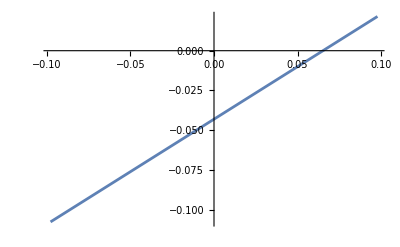

```mathematica
Plot[KL,{x,-0.09781805564359501,0.09781805564359501}]
```

```mathematica
Plot[KL,{x,-0.09781805564359501,0.09781805564359501},PlotTheme->Automatic]
```

-Graphics-

```mathematica
Plot[KL,{x,-0.09781805564359501,0.09781805564359501},PlotTheme->Automatic]
```

-Graphics-

```mathematica
(*K矩阵无拟合*)



(*LQR权重矩阵*)
(*Subscript[Q, lqr]=DiagonalMatrix[{3000,3000,5000,200,20000,500,20000,500,20000,800}];*)
Subscript[R, lqr]=DiagonalMatrix[{200,200,10,10}];
Subscript[Q, lqr]=DiagonalMatrix[{2000,4000,5000,200,30000,500,30000,500,30000,800}];
(*Subscript[Q, lqr]=DiagonalMatrix[{1000,2000,5000,100,40000,1500,40000,1500,10000,500}];9.8*)

(*Subscript[Q, lqr]=DiagonalMatrix[{2000,2000,5000,100,60000,2000,60000,2000,20000,800}];*)

(*由五连杆和电机定子的质量分布参数算出两腿质量分布参数*)
Subscript[l, l]=0.20;(*设置左腿长*)
Subscript[l, r]=0.20;(*设置右腿长*)
Get["VMCsolution.m",Path->NotebookDirectory[]];
para=LegCalcu[Subscript[l, l],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]},{Subscript[l, 1],Subscript[l, 2],Subscript[l, 3],Subscript[l, 4]},{Subscript[I, 1],Subscript[I, 2],Subscript[I, 3],Subscript[I, 4],Subscript[I, wm]},{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3],Subscript[m, 4],Subscript[m, wm]}];
Subscript[l, w,l]=para[[1]];Subscript[I, l,l]=para[[2]];Subscript[m, l]=para[[3]];Subscript[l, b,l]=Subscript[l, l]-Subscript[l, w,l];
para=LegCalcu[Subscript[l, r],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]},{Subscript[l, 1],Subscript[l, 2],Subscript[l, 3],Subscript[l, 4]},{Subscript[I, 1],Subscript[I, 2],Subscript[I, 3],Subscript[I, 4],Subscript[I, wm]},{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3],Subscript[m, 4],Subscript[m, wm]}];
Subscript[l, w,r]=para[[1]];Subscript[I, l,r]=para[[2]];Subscript[l, b,r]=Subscript[l, r]-Subscript[l, w,r];
(*LQR计算*)
Subscript[A, op]=Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op]=Import[NotebookDirectory[]<>"B_op.wdx"];    
Subscript[A, op]=SparseArray[Subscript[A, op]];
Subscript[B, op]=SparseArray[Subscript[B, op]];
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr]
```

{{-1.87217,-4.10177,-3.26863,-0.862163,-12.0747,-2.00547,-7.33564,-1.31043,-5.5946,-1.5454},{-1.87217,-4.10177,3.26863,0.862163,-7.33564,-1.31043,-12.0747,-2.00547,-5.5946,-1.5454},{5.46805,11.2356,-6.02667,-1.64378,52.2473,7.68457,-8.73536,-0.316438,-31.0053,-4.84195},{5.46805,11.2356,6.02667,1.64378,-8.73536,-0.316438,52.2473,7.68457,-31.0053,-4.84195}}

```mathematica
Transpose[%31]
```

{{-2.26865,-2.26865,3.37629,3.37629},{-5.00187,-5.00187,6.99802,6.99802},{-3.5492,3.5492,-5.52483,5.52483},{-0.913247,0.913247,-1.54818,1.54818},{-15.3219,-8.12304,36.2855,-7.97633},{-2.86113,-1.5128,6.37322,-0.917794},{-8.12304,-15.3219,-7.97633,36.2855},{-1.5128,-2.86113,-0.917794,6.37322},{-5.81091,-5.81091,-23.2914,-23.2914},{-1.65793,-1.65793,-3.96657,-3.96657}}

```mathematica
Transpose[%32]
```

{{-2.26865,-5.00187,-3.5492,-0.913247,-15.3219,-2.86113,-8.12304,-1.5128,-5.81091,-1.65793},{-2.26865,-5.00187,3.5492,0.913247,-8.12304,-1.5128,-15.3219,-2.86113,-5.81091,-1.65793},{3.37629,6.99802,-5.52483,-1.54818,36.2855,6.37322,-7.97633,-0.917794,-23.2914,-3.96657},{3.37629,6.99802,5.52483,1.54818,-7.97633,-0.917794,36.2855,6.37322,-23.2914,-3.96657}}

```mathematica
Transpose[%33]
```

{{-2.26865,-2.26865,3.37629,3.37629},{-5.00187,-5.00187,6.99802,6.99802},{-3.5492,3.5492,-5.52483,5.52483},{-0.913247,0.913247,-1.54818,1.54818},{-15.3219,-8.12304,36.2855,-7.97633},{-2.86113,-1.5128,6.37322,-0.917794},{-8.12304,-15.3219,-7.97633,36.2855},{-1.5128,-2.86113,-0.917794,6.37322},{-5.81091,-5.81091,-23.2914,-23.2914},{-1.65793,-1.65793,-3.96657,-3.96657}}

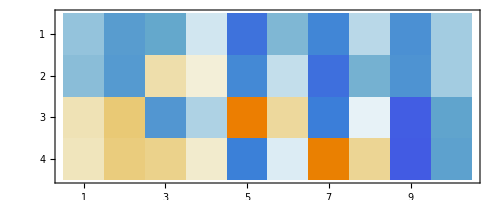

```mathematica
MatrixPlot[%157]
```

```mathematica
MatrixPlot[%157,PlotTheme->Automatic]
```

-Graphics-

```mathematica
MatrixPlot[{{-2.291797275736921,-4.985911491110787,-3.5724193404209257,-0.9168367489123382,-14.897756279582145,-2.4480664872060696,-7.846602465899438,-1.449307713553363,-5.61107340845029,-1.6255866736641178},{-2.2917972757369305,-4.985911491110802,3.5724193404209146,0.9168367489125866,-7.846602465896648,-1.4493077135528705,-14.89775627958512,-2.4480664872065767,-5.611073408450135,-1.6255866736641158},{3.2569140842137,6.626448840305173,-5.4114370015739235,-1.530920135103711,35.09969648914147,5.092869447299069,-9.389037216638167,-0.7690246433330131,-23.65124282930083,-4.0556822578321885},{3.256914084213686,6.626448840305116,5.41143700160286,1.5309201351061326,-9.389037216611827,-0.7690246433336337,35.09969648911576,5.092869447299707,-23.651242829301502,-4.05568225783221}},PlotTheme->Automatic]
```

-Graphics-

```mathematica
(*K矩阵腿长拟合动态显示*)
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{100,200,800,30,100,10,100,10,10000,800}];
Subscript[R, lqr]=DiagonalMatrix[{20,20,100,100}];
(*由五连杆和电机定子的质量分布参数算出两腿质量分布参数*)
Get["VMCsolution.m",Path->NotebookDirectory[]];
SystemCalcu[Ll_,Lr_]:=(
Module[{},
Subscript[l, l]=Ll;Subscript[l, r]=Lr;
para=LegCalcu[Ll,{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]},{Subscript[l, 1],Subscript[l, 2],Subscript[l, 3],Subscript[l, 4]},{Subscript[I, 1],Subscript[I, 2],Subscript[I, 3],Subscript[I, 4],Subscript[I, wm]},{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3],Subscript[m, 4],Subscript[m, wm]}];
Subscript[l, w,l]=para[[1]];Subscript[I, l,l]=para[[2]];Subscript[m, l]=para[[3]];Subscript[l, b,l]=Ll-Subscript[l, w,l];
para=LegCalcu[Lr,{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]},{Subscript[l, 1],Subscript[l, 2],Subscript[l, 3],Subscript[l, 4]},{Subscript[I, 1],Subscript[I, 2],Subscript[I, 3],Subscript[I, 4],Subscript[I, wm]},{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3],Subscript[m, 4],Subscript[m, wm]}];
Subscript[l, w,r]=para[[1]];Subscript[I, l,r]=para[[2]];Subscript[l, b,r]=Lr-Subscript[l, w,r];
(*LQR计算*)
Subscript[A, op]=Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op]=Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[A, op]=SparseArray[Subscript[A, op]];
Subscript[B, op]=SparseArray[Subscript[B, op]];
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr];
Return[Subscript[K, lqr]];
];
);
Manipulate[SystemCalcu[Ll,Lr],{{Ll,0.25},0.1,0.4},{{Lr,0.25},0.1,0.4}](*显示具体数值*)
```

```mathematica
(*K矩阵腿长拟合多项式提取*)
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{100,200,800,30,100,10,100,10,10000,800}];
Subscript[R, lqr]=DiagonalMatrix[{20,20,100,100}];
(*循环迭代*)
sampleNum=21;(*循环次数*)
paramNum=40;(*变量个数*)
Kt=Array[0,{sampleNum,sampleNum}];
Xt=Array[0,{sampleNum,sampleNum}];
Get["VMCsolution.m",Path->NotebookDirectory[]];
Do[
Do[
(*输入量控制*)
Subscript[l, l]=0.10+0.2*(cnt1)/sampleNum;
Subscript[l, r]=0.10+0.2*(cnt2)/sampleNum;
(*由五连杆和电机定子的质量分布参数算出两腿质量分布参数*)
para=LegCalcu[Subscript[l, l],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]},{Subscript[l, 1],Subscript[l, 2],Subscript[l, 3],Subscript[l, 4]},{Subscript[I, 1],Subscript[I, 2],Subscript[I, 3],Subscript[I, 4],Subscript[I, wm]},{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3],Subscript[m, 4],Subscript[m, wm]}];
Subscript[l, w,l]=para[[1]];Subscript[I, l,l]=para[[2]];Subscript[m, l]=para[[3]];Subscript[l, b,l]=Subscript[l, l]-Subscript[l, w,l];
para=LegCalcu[Subscript[l, r],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]},{Subscript[l, 1],Subscript[l, 2],Subscript[l, 3],Subscript[l, 4]},{Subscript[I, 1],Subscript[I, 2],Subscript[I, 3],Subscript[I, 4],Subscript[I, wm]},{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3],Subscript[m, 4],Subscript[m, wm]}];
Subscript[l, w,r]=para[[1]];Subscript[I, l,r]=para[[2]];Subscript[l, b,r]=Subscript[l, r]-Subscript[l, w,r];
(*LQR计算*)
Subscript[A, op] = Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op] = Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[A, op]=SparseArray[Subscript[A, op]];
Subscript[B, op]=SparseArray[Subscript[B, op]];
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr];
(*数据记录*)
Kt[[cnt1,cnt2]] = Subscript[K, lqr];
Xt[[cnt1,cnt2]]={Subscript[l, l],Subscript[l, r]};
,{cnt1,sampleNum}];
,{cnt2,sampleNum}];
(*多项式拟合*)
kArray=Array[0,{paramNum}];Do[Do[kArray[[(i-1)*10+j]]=Kt[[All,All,i,j]],{j,10}],{i,4}];
(*将条件值与参数值配对*)
Kxy=Array[0,{paramNum,sampleNum*sampleNum}];
Do[Do[Do[Kxy[[i,(j-1)*sampleNum+k]]={Xt[[j,k,1]],Xt[[j,k,2]],kArray[[i,j,k]]},{k,sampleNum}],{j,sampleNum}],{i,paramNum}];
(*分别对各个参数进行多项式拟合*)
Kpoly = Array[0, {paramNum}];
Do[Kpoly[[i]]= Fit[Kxy[[i]],{1,x,x^2,y,y^2,x*y},{x,y}],{i,paramNum}];
(*将多项式系数整合成一个矩阵*)
kPolyMatrix = Array[0,{40}];
Do[kPolyMatrix[[i]]=CoefficientList[Kpoly[[i]],{x,y}],{i,paramNum}];
(*多项式拟合曲线*)
KT = Array[0, {paramNum}];
KTT=Array[0,{paramNum}];
Do[KT[[plotcnt]] = Plot3D[Kpoly[[plotcnt]], {x, Xt[[1,1,1]], Xt[[sampleNum,sampleNum,1]]},{y, Xt[[1,1,2]], Xt[[sampleNum,sampleNum,2]]},Axes->{True,True,True}, AxesLabel->{"l_l", "l_r",Subscript[K, plotcnt]}];
,{plotcnt, 1,paramNum}];
KLTGraph = GraphicsGrid[{{KT[[1]],KT[[11]],KT[[21]],KT[[31]]},{KT[[2]],KT[[12]],KT[[22]],KT[[32]]},{KT[[3]],KT[[13]],KT[[23]],KT[[33]]},{KT[[4]],KT[[14]],KT[[24]],KT[[34]]},{KT[[5]],KT[[15]],KT[[25]],KT[[35]]},{KT[[6]],KT[[16]],KT[[26]],KT[[36]]},{KT[[7]],KT[[17]],KT[[27]],KT[[37]]},{KT[[8]],KT[[18]],KT[[28]],KT[[38]]},{KT[[9]],KT[[19]],KT[[29]],KT[[39]]},{KT[[10]],KT[[20]],KT[[30]],KT[[40]]}}, Frame->All,ImageSize->Full];
(*============================================数据输出===========================================*)
Print[Kpoly];
Print[kPolyMatrix];(*拟合多项式升幂排列*)
Show[KLTGraph](*多项式拟合曲线图*)
```

{-1.50521-0.0947795 x+2.25187 x^2-0.297581 y-3.46691 x y+1.7195 y^2,-3.2374+1.69947 x+1.93118 x^2-0.604944 y-8.36906 x y+3.68256 y^2,-4.58451+23.0411 x-35.7573 x^2-3.29834 y+20.8055 x y-1.74883 y^2,-1.01722+7.78084 x-12.0255 x^2-1.09305 y+6.75681 x y-0.307284 y^2,-2.59861-82.5389 x+102.31 x^2+7.24318 y-96.4323 x y+14.3029 y^2,-1.25193-7.63048 x+9.3276 x^2+0.939706 y-13.7727 x y+2.23029 y^2,-5.85245+59.8311 x-100.409 x^2-12.9176 y+115.263 x y-9.8191 y^2,-0.915861+10.0255 x-13.7556 x^2-3.25181 y+7.43376 x y+1.35827 y^2,-5.37686+16.2586 x+0.733271 x^2+1.73417 y-26.6005 x y+4.04648 y^2,-2.09713+6.87844 x-0.429078 x^2+0.459176 y-11.1313 x y+2.03608 y^2,-1.50521-0.297581 x+1.7195 x^2-0.0947795 y-3.46691 x y+2.25187 y^2,-3.2374-0.604944 x+3.68256 x^2+1.69947 y-8.36906 x y+1.93118 y^2,4.58451+3.29834 x+1.74883 x^2-23.0411 y-20.8055 x y+35.7573 y^2,1.01722+1.09305 x+0.307284 x^2-7.78084 y-6.75681 x y+12.0255 y^2,-5.85245-12.9176 x-9.8191 x^2+59.8311 y+115.263 x y-100.409 y^2,-0.915861-3.25181 x+1.35827 x^2+10.0255 y+7.43376 x y-13.7556 y^2,-2.59861+7.24318 x+14.3029 x^2-82.5389 y-96.4323 x y+102.31 y^2,-1.25193+0.939706 x+2.23029 x^2-7.63048 y-13.7727 x y+9.3276 y^2,-5.37686+1.73417 x+4.04648 x^2+16.2586 y-26.6005 x y+0.733271 y^2,-2.09713+0.459176 x+2.03608 x^2+6.87844 y-11.1313 x y-0.429078 y^2,0.204227-2.80685 x+3.79536 x^2+2.17237 y+0.0815455 x y-3.21514 y^2,0.405015-6.16084 x+8.62444 x^2+4.81512 y+0.0791303 x y-7.17406 y^2,-1.02566-3.85695 x+9.12493 x^2-2.9701 y-2.69276 x y+5.5339 y^2,-0.519274-0.91573 x+2.35994 x^2-0.724588 y-0.606744 x y+1.25477 y^2,1.73541+18.3295 x-36.561 x^2+14.4482 y+20.8337 x y-26.1614 y^2,0.673793-1.05198 x+0.254012 x^2+2.56337 y+2.3171 x y-4.27995 y^2,-0.732098-18.8895 x+39.3244 x^2-14.4519 y-19.9669 x y+21.7411 y^2,-0.431308-3.1787 x+6.2188 x^2+1.01953 y-2.72756 x y-1.05428 y^2,-6.39342-9.14781 x+11.1429 x^2+7.31168 y-0.721045 x y-7.68526 y^2,-1.96564-4.16744 x+5.35293 x^2+3.36939 y-0.301193 x y-3.85301 y^2,0.204227+2.17237 x-3.21514 x^2-2.80685 y+0.0815455 x y+3.79536 y^2,0.405015+4.81512 x-7.17406 x^2-6.16084 y+0.0791303 x y+8.62444 y^2,1.02566+2.9701 x-5.5339 x^2+3.85695 y+2.69276 x y-9.12493 y^2,0.519274+0.724588 x-1.25477 x^2+0.91573 y+0.606744 x y-2.35994 y^2,-0.732098-14.4519 x+21.7411 x^2-18.8895 y-19.9669 x y+39.3244 y^2,-0.431308+1.01953 x-1.05428 x^2-3.1787 y-2.72756 x y+6.2188 y^2,1.73541+14.4482 x-26.1614 x^2+18.3295 y+20.8337 x y-36.561 y^2,0.673793+2.56337 x-4.27995 x^2-1.05198 y+2.3171 x y+0.254012 y^2,-6.39342+7.31168 x-7.68526 x^2-9.14781 y-0.721045 x y+11.1429 y^2,-1.96564+3.36939 x-3.85301 x^2-4.16744 y-0.301193 x y+5.35293 y^2}

{{{-1.50521,-0.297581,1.7195},{-0.0947795,-3.46691,0},{2.25187,0,0}},{{-3.2374,-0.604944,3.68256},{1.69947,-8.36906,0},{1.93118,0,0}},{{-4.58451,-3.29834,-1.74883},{23.0411,20.8055,0},{-35.7573,0,0}},{{-1.01722,-1.09305,-0.307284},{7.78084,6.75681,0},{-12.0255,0,0}},{{-2.59861,7.24318,14.3029},{-82.5389,-96.4323,0},{102.31,0,0}},{{-1.25193,0.939706,2.23029},{-7.63048,-13.7727,0},{9.3276,0,0}},{{-5.85245,-12.9176,-9.8191},{59.8311,115.263,0},{-100.409,0,0}},{{-0.915861,-3.25181,1.35827},{10.0255,7.43376,0},{-13.7556,0,0}},{{-5.37686,1.73417,4.04648},{16.2586,-26.6005,0},{0.733271,0,0}},{{-2.09713,0.459176,2.03608},{6.87844,-11.1313,0},{-0.429078,0,0}},{{-1.50521,-0.0947795,2.25187},{-0.297581,-3.46691,0},{1.7195,0,0}},{{-3.2374,1.69947,1.93118},{-0.604944,-8.36906,0},{3.68256,0,0}},{{4.58451,-23.0411,35.7573},{3.29834,-20.8055,0},{1.74883,0,0}},{{1.01722,-7.78084,12.0255},{1.09305,-6.75681,0},{0.307284,0,0}},{{-5.85245,59.8311,-100.409},{-12.9176,115.263,0},{-9.8191,0,0}},{{-0.915861,10.0255,-13.7556},{-3.25181,7.43376,0},{1.35827,0,0}},{{-2.59861,-82.5389,102.31},{7.24318,-96.4323,0},{14.3029,0,0}},{{-1.25193,-7.63048,9.3276},{0.939706,-13.7727,0},{2.23029,0,0}},{{-5.37686,16.2586,0.733271},{1.73417,-26.6005,0},{4.04648,0,0}},{{-2.09713,6.87844,-0.429078},{0.459176,-11.1313,0},{2.03608,0,0}},{{0.204227,2.17237,-3.21514},{-2.80685,0.0815455,0},{3.79536,0,0}},{{0.405015,4.81512,-7.17406},{-6.16084,0.0791303,0},{8.62444,0,0}},{{-1.02566,-2.9701,5.5339},{-3.85695,-2.69276,0},{9.12493,0,0}},{{-0.519274,-0.724588,1.25477},{-0.91573,-0.606744,0},{2.35994,0,0}},{{1.73541,14.4482,-26.1614},{18.3295,20.8337,0},{-36.561,0,0}},{{0.673793,2.56337,-4.27995},{-1.05198,2.3171,0},{0.254012,0,0}},{{-0.732098,-14.4519,21.7411},{-18.8895,-19.9669,0},{39.3244,0,0}},{{-0.431308,1.01953,-1.05428},{-3.1787,-2.72756,0},{6.2188,0,0}},{{-6.39342,7.31168,-7.68526},{-9.14781,-0.721045,0},{11.1429,0,0}},{{-1.96564,3.36939,-3.85301},{-4.16744,-0.301193,0},{5.35293,0,0}},{{0.204227,-2.80685,3.79536},{2.17237,0.0815455,0},{-3.21514,0,0}},{{0.405015,-6.16084,8.62444},{4.81512,0.0791303,0},{-7.17406,0,0}},{{1.02566,3.85695,-9.12493},{2.9701,2.69276,0},{-5.5339,0,0}},{{0.519274,0.91573,-2.35994},{0.724588,0.606744,0},{-1.25477,0,0}},{{-0.732098,-18.8895,39.3244},{-14.4519,-19.9669,0},{21.7411,0,0}},{{-0.431308,-3.1787,6.2188},{1.01953,-2.72756,0},{-1.05428,0,0}},{{1.73541,18.3295,-36.561},{14.4482,20.8337,0},{-26.1614,0,0}},{{0.673793,-1.05198,0.254012},{2.56337,2.3171,0},{-4.27995,0,0}},{{-6.39342,-9.14781,11.1429},{7.31168,-0.721045,0},{-7.68526,0,0}},{{-1.96564,-4.16744,5.35293},{3.36939,-0.301193,0},{-3.85301,0,0}}}

-Graphics-